## Dependence on the output

```mathematica
measureState=4;(*1~4*)
```

```mathematica
x1lst={0,1,0,1};
x2lst={0,0,1,1};
```

```mathematica
e1=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5);
e2=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5);
e3=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5);
e4=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5)+0.5 γ(-1)^2;
e5=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5)+0.5 γ(1)^2;
e6=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5)+0.5 γ(1)^2;
e7=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5)+0.5 γ(1)^2;
e8=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5);
```

```mathematica
ee1=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5);
ee2=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5);
ee3=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5);
ee4=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5);
ee5=-h (x1-0.5) (-0.5)-h (x2-0.5) (-0.5);
ee6=-h (x1-0.5) (1-0.5)-h (x2-0.5) (-0.5);
ee7=-h (x1-0.5) (-0.5)-h (x2-0.5) (1-0.5);
ee8=-h (x1-0.5) (1-0.5)-h (x2-0.5) (1-0.5);
```

```mathematica
W={{0,Exp[e2],Exp[e3],0,Exp[e5],0,0,0},
{Exp[e1],0,0,Exp[e4],0,Exp[e6],0,0},
{Exp[e1],0,0,Exp[e4],0,0,Exp[e7],0},
{0,Exp[e2],Exp[e3],0,0,0,0,Exp[e8]},
{Exp[e1],0,0,0,0,Exp[e6],Exp[e7],0},
{0,Exp[e2],0,0,Exp[e5],0,0,Exp[e8]},
{0,0,Exp[e3],0,Exp[e5],Exp[e6],0,0},
{0,0,0,Exp[e4],0,Exp[e6],Exp[e7],0}};
```

```mathematica
Wneq={{0,Exp[ee2],Exp[ee3],0,Exp[ee5+γ(1-1/2)],0,0,0},
{Exp[ee1],0,0,Exp[ee4],0,Exp[ee6+γ(1-1/2)],0,0},
{Exp[ee1],0,0,Exp[ee4],0,0,Exp[ee7+γ(1-1/2)],0},
{0,Exp[ee2],Exp[ee3],0,0,0,0,Exp[ee8+γ(-1/2)]},
{Exp[ee1+γ(-1/2)],0,0,0,0,Exp[ee6],Exp[ee7],0},
{0,Exp[ee2+γ(-1/2)],0,0,Exp[ee5],0,0,Exp[ee8]},
{0,0,Exp[ee3+γ(-1/2)],0,Exp[ee5],Exp[ee6],0,0},
{0,0,0,Exp[ee4+γ(1-1/2)],0,Exp[ee6],Exp[ee7],0}};
```

```mathematica
For[i=1,i<=8,i++,
W[[i,i]]=-Sum[W[[j,i]],{j,1,8}];
Wneq[[i,i]]=-Sum[Wneq[[j,i]],{j,1,8}];]
(*以上为master equation matrix信息录入*)
```

```mathematica
(W[[1,2]]W[[2,4]]W[[4,3]]W[[3,1]])/(W[[2,1]]W[[4,2]]W[[3,4]]W[[1,3]])//FullSimplify
(Wneq[[1,2]]Wneq[[2,4]]Wneq[[4,3]]Wneq[[3,1]])/(Wneq[[2,1]]Wneq[[4,2]]Wneq[[3,4]]Wneq[[1,3]])//FullSimplify
```

1.

1.

```mathematica
(W[[1,5]]W[[5,6]]W[[6,8]] W[[8,4]]W[[4,3]]W[[3,1]])/(W[[5,1]]W[[6,5]]W[[8,6]] W[[4,8]]W[[3,4]]W[[1,3]])//FullSimplify
(Wneq[[1,5]]Wneq[[5,6]]Wneq[[6,8]] Wneq[[8,4]]Wneq[[4,3]]Wneq[[3,1]])/(Wneq[[5,1]]Wneq[[6,5]]Wneq[[8,6]] Wneq[[4,8]]Wneq[[3,4]]Wneq[[1,3]])//FullSimplify
```

1.

ⅇ^(2 γ)

```mathematica
(*以下代入环境信号x_1,x_2*)
λvec=Eigenvalues[W/.h->6/.γ->60/.{x1->x1lst[[measureState]],x2->x2lst[[measureState]]}];
evec=Eigenvectors[W/.h->6/.γ->60/.{x1->x1lst[[measureState]],x2->x2lst[[measureState]]}];
λvecNeq=Eigenvalues[Wneq/.h->6/.γ->60/.{x1->x1lst[[measureState]],x2->x2lst[[measureState]]}];
evecNeq=Eigenvectors[Wneq/.h->6/.γ->60/.{x1->x1lst[[measureState]],x2->x2lst[[measureState]]}];
pss=evec[[8]]/Total[evec[[8]]];
pssNeq=evecNeq[[8]]/Total[evecNeq[[8]]];
(*计算初始状态的本征态叠加系数*)
zeroterms=Cases[Table[i,{i,1,7}],Except[5-measureState]];
csub1=Flatten[NSolve[Flatten[Join[{pss[[5-measureState]]+Sum[evec[[j]][[5-measureState]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]]
cNeq1=Flatten[NSolve[Flatten[Join[{pssNeq[[5-measureState]]+Sum[evecNeq[[j]][[5-measureState]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]]

zeroterms=Cases[Table[i,{i,1,7}],Except[9-measureState]];
csub2=If[measureState!=1,Flatten[NSolve[Flatten[Join[{pss[[9-measureState]]+Sum[evec[[j]][[9-measureState]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]],Flatten[NSolve[Flatten[Join[{pss[[8]]+Sum[evec[[j]][[8]] c[j],{j,1,7}]==1,Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]]
cNeq2=If[measureState!=1,Flatten[NSolve[Flatten[Join[{pssNeq[[9-measureState]]+Sum[evecNeq[[j]][[9-measureState]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,zeroterms}]}]],Table[c[j],{j,1,7}]]],Flatten[NSolve[Flatten[Join[{pssNeq[[8]]+Sum[evecNeq[[j]][[8]] c[j],{j,1,7}]==1,Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==0,{i,2,7}]}]],Table[c[j],{j,1,7}]]]]
```

{c[1]→3.53948×10^-14,c[2]→1.42675×10^-13,c[3]→-5.61451×10^-13,c[4]→-2.77195×10^-17,c[5]→1.16712,c[6]→0.0292078,c[7]→1.02365}

{c[1]→-2.42578×10^-16,c[2]→-8.15903×10^-18,c[3]→-5.75267×10^-18,c[4]→-2.00692×10^-22,c[5]→-1.20381,c[6]→0.018506,c[7]→1.1853}

{c[1]→-1.14779,c[2]→-0.303642,c[3]→0.689086,c[4]→2.3255×10^-13,c[5]→0.492652,c[6]→-0.0235453,c[7]→0.741874}

{c[1]→-1.41421,c[2]→1.95851×10^-13,c[3]→2.77359×10^-13,c[4]→-4.98101×10^-17,c[5]→-1.20381,c[6]→0.018506,c[7]→1.1853}

General::munfl: Exp[-1.39572×10^11] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9.15983×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.28246×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

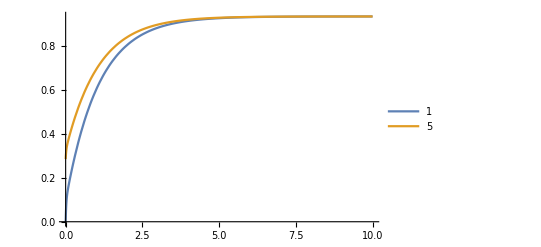

General::munfl: Exp[-4.5995×10^10] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.28996×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

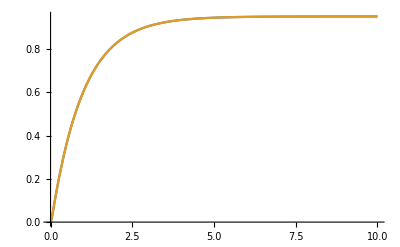

```mathematica
(*以下为绘制演化图*)
Plot[{(pss[[measureState]]+Sum[evec[[j]][[measureState]] c[j]Exp[λvec[[j]] t],{j,1,7}]+pss[[measureState+4]]+Sum[evec[[j]][[measureState+4]] c[j]Exp[λvec[[j]] t],{j,1,7}])/.csub1,(pss[[measureState]]+Sum[evec[[j]][[measureState]] c[j]Exp[λvec[[j]] t],{j,1,7}]+pss[[measureState+4]]+Sum[evec[[j]][[measureState+4]] c[j]Exp[λvec[[j]] t],{j,1,7}])/.csub2},{t,10^-5,10},PlotRange->All,PlotLegends->{5-measureState,9-measureState}]
Plot[{(pssNeq[[measureState]]+Sum[evecNeq[[j]][[measureState]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}]+pssNeq[[measureState+4]]+Sum[evecNeq[[j]][[measureState+4]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}])/.cNeq1,(pssNeq[[measureState]]+Sum[evecNeq[[j]][[measureState]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}]+pssNeq[[measureState+4]]+Sum[evecNeq[[j]][[measureState+4]] c[j]Exp[λvecNeq[[j]] t],{j,1,7}])/.cNeq2},{t,10^-5,10},PlotRange->All,PlotLegends->{5-measureState,9-measureState}]
```

```mathematica
λvec
```

{-8950.26,-593.904,-457.609,-29.6092,-14.8213,-2.74884,-1.30149,1.57031×10^-14}

## Time dependent perturbation

```mathematica
expvec[t_]:=Exp[λvec t];
Clear[σ,p1,p2]
σ=0.2;
pSHOT=0.001;
t0old=0;
p00list={};
counter=0;
cOLD=Flatten[NSolve[Flatten[Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==pss[[i]],{i,1,7}]]]];
OLDstate=pss;
pTOT=pss;
count=0;

For[expt=0,expt<500,expt=expt+0.01,

t=expt;
count++;

p1=First[Flatten[RandomVariate[UniformDistribution[1],1]]];
p2=First[Flatten[RandomVariate[UniformDistribution[1],1]]];
shot=First[Flatten[RandomVariate[NormalDistribution[0,Sqrt[σ]],1]]];

ϵ1=If[Mod[count,100]==0,Abs[shot],0];(*控制加shot的时机*)

(*ϵ1=If[p1<=pSHOT,shot,0];*)

(*ϵ=If[p1<=pSHOT&&counter==0,shot,0];*)

n=If[ϵ1!=0&&p2<=0.5,4,8];(*控制加shot的态；需根据当前环境信号调整*)

(*counter=If[ϵ!=0,counter+1,counter];*)

(*Print[p1" ",p2" ",shot" ",ϵ" ",n];*)
(*Print[pTOT[[n]]+ϵ1];*)

ϵ=If[pTOT[[n]]+ϵ1<0,-pTOT[[n]]+10^-8,ϵ1];

NEWstate=If[ϵ!=0,(pTOT+ReplacePart[ConstantArray[0,8],n->ϵ])/Total[pTOT+ReplacePart[ConstantArray[0,8],n->ϵ]],OLDstate];
cNEW=If[ϵ!=0,Flatten[NSolve[Flatten[Table[pss[[i]]+Sum[evec[[j]][[i]] c[j],{j,1,7}]==NEWstate[[i]],{i,1,7}]],Table[c[j],{j,1,7}]]],cOLD];
t0=If[ϵ!=0,t,t0old];

p00=pss[[4]]+Sum[evec[[j]][[4]] c[j]expvec[t-t0][[j]],{j,1,7}]+pss[[8]]+Sum[evec[[j]][[8]] c[j] expvec[t-t0][[j]],{j,1,7}]/.cNEW;(*需根据当前环境信号调整*)
pTOT=pss+Sum[evec[[j]] c[j]expvec[t-t0][[j]],{j,1,7}]/.cNEW;

p00list=Append[p00list,{t,p00}];

(*Print[pss[[1]]+pss[[5]]" ",p00" ",t0];*)

t0old=t0;
cOLD=cNEW;
OLDstate=NEWstate;

(*Print[NEWstate];
Print[pTOT];
Print[t0"___",ϵ"___",cOLD];*)
]
```

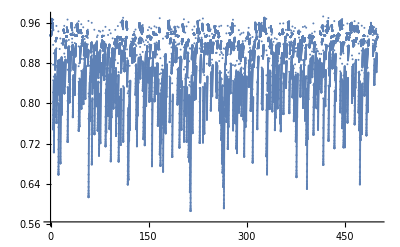

26940

7861

50001

20126

1745

50001

```mathematica
ListPlot[p00list,PlotRange->All,ImageSize->Full,PlotMarkers->{Automatic,2}]
Count[p00list[[All,2]],u_/;u<=0.9]
Count[p00list[[All,2]],u_/;u<=0.8]
Length[p00list[[All,2]]]
```

```mathematica
expvecNeq[t_]:=Exp[λvecNeq t];
```

```mathematica
Clear[σ,p1,p2]
σ=0.2;
pSHOT=0.001;
t0old=0;
p00list={};
counter=0;
cOLD=Flatten[NSolve[Flatten[Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==pssNeq[[i]],{i,1,7}]]]];
OLDstate=pssNeq;
pTOT=pssNeq;
count=0;

For[expt=0,expt<500,expt=expt+0.01,

t=expt;
count++;
p1=First[Flatten[RandomVariate[UniformDistribution[1],1]]];
p2=First[Flatten[RandomVariate[UniformDistribution[1],1]]];
shot=First[Flatten[RandomVariate[NormalDistribution[0,Sqrt[σ]],1]]];
ϵ1=If[Mod[count,100]==0,Abs[shot],0];

(*ϵ1=If[p1<=pSHOT,shot,0];*)

(*ϵ=If[p1<=pSHOT&&counter==0,shot,0];*)

n=If[ϵ1!=0&&p2<=0.5,4,8];(*需根据当前环境信号调整*)

(*counter=If[ϵ!=0,counter+1,counter];*)

(*Print[p1" ",p2" ",shot" ",ϵ" ",n];*)
(*Print[pTOT[[n]]+ϵ1];*)

ϵ=If[pTOT[[n]]+ϵ1<0,-pTOT[[n]]+10^-8,ϵ1];

NEWstate=If[ϵ!=0,(pTOT+ReplacePart[ConstantArray[0,8],n->ϵ])/Total[pTOT+ReplacePart[ConstantArray[0,8],n->ϵ]],OLDstate];(*计算shot后的分布*)
cNEW=If[ϵ!=0,Flatten[NSolve[Flatten[Table[pssNeq[[i]]+Sum[evecNeq[[j]][[i]] c[j],{j,1,7}]==NEWstate[[i]],{i,1,7}]],Table[c[j],{j,1,7}]]],cOLD];
t0=If[ϵ!=0,t,t0old];

p00=pssNeq[[4]]+Sum[evecNeq[[j]][[4]] c[j]expvecNeq[t-t0][[j]],{j,1,7}]+pssNeq[[8]]+Sum[evecNeq[[j]][[8]] c[j] expvecNeq[t-t0][[j]],{j,1,7}]/.cNEW;(*需根据当前环境信号调整*)
pTOT=pssNeq+Sum[evecNeq[[j]] c[j]expvec[t-t0][[j]],{j,1,7}]/.cNEW;

p00list=Append[p00list,{t,p00}];

(*Print[pss[[1]]+pss[[5]]" ",p00" ",t0];*)

t0old=t0;
cOLD=cNEW;
OLDstate=NEWstate;

(*Print[NEWstate];
Print[pTOT];
Print[t0"___",ϵ"___",cOLD];*)
](*For循环结束*)
```

General::munfl: -5.34076×10^-308+5.34085×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.16394×10^-299 (-1.23442×10^-9) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -5.34076×10^-308+5.34085×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

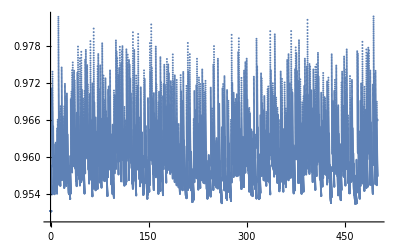

0

0

50001

0

0

50001

```mathematica
ListPlot[p00list,PlotRange->All,ImageSize->Full,PlotMarkers->{Automatic,2}]
Count[p00list[[All,2]],u_/;u<=0.9]
Count[p00list[[All,2]],u_/;u<=0.8]
Length[p00list[[All,2]]]
```